```mathematica
(*One node implementation - Ideal controller - Time varying adjacency matrices*)
(*Make sure to run the code on a clean kernel*)
Quit[]
```

-Graphics- | -Graphics-

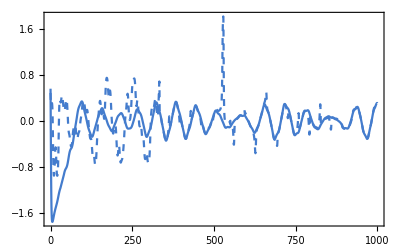
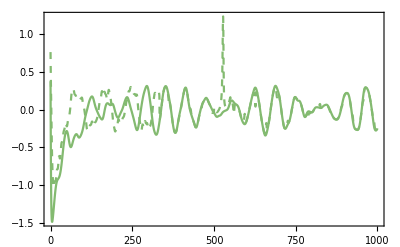
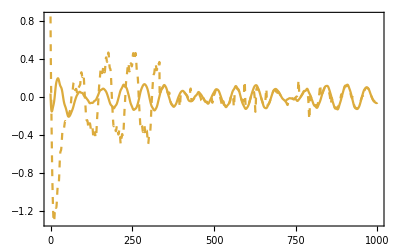
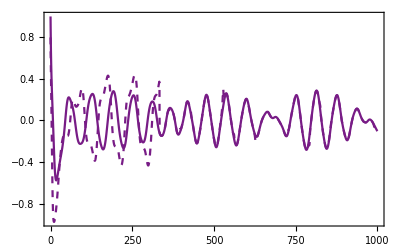
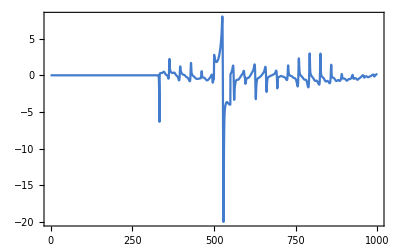
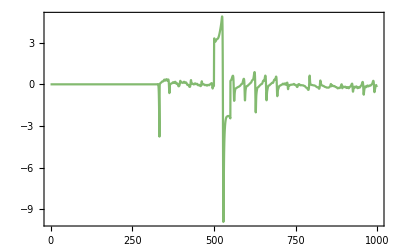
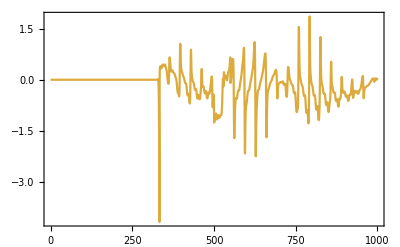
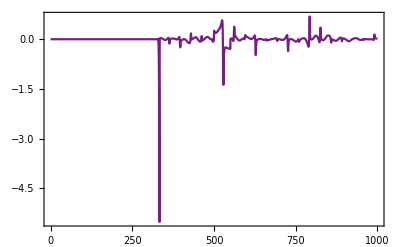

```mathematica
(*----------------------------------------------------*)
(*------------------- GENERAL SETUP -------------------*)
ClearAll["Global`*"];

(*To format figures:*)
cm=72/2.54;
sz = Round[4.5 cm];(*size for figures*)

(*Random Adjacency matrix:*)
RandomAdjacency[n_,selfloops_:0]:=Module[{A,B,out},(*By default, RandomAdjacency returns a positively weighted adjacency matrix without self loops*)
A=RandomReal[{0,1},{n,n}];
If[selfloops==1,
out=A,
out=A-DiagonalMatrix[Diagonal[A]]]
];

(*Juarez&Franci algorithm:*)
u=1; (*real part of the leading eigenvalue*)
RythmicAdjacency[n_,density_:0.5]:=Module[{ρ,θ,w,μ,Q,out},(*density for the nonzero elements of the complement basis in Q=[w,Conjugate[w],B]*)
ρ=RandomReal[{1/3,1},n];(*relative amplitudes not too small*)
ρ[[1]]=1;
θ=RandomReal[{0,2 Pi},n];(*The probability of Subscript[θ, i]={0,π} is zero*)
w=ρ*Exp[I θ];
μ=RandomReal[{0,9/10 u},n]; (*To ensure that the rest of eigenvalues have smaller real part*)
μ[[1]]=u+RandomReal[{1/100,1/10}]I;(*just to avoid high frequencies*)
μ[[2]]=Conjugate[μ[[1]]];
out={};
Q={};
tries=0;
While[True,
Q={};
(*Q=RandomReal[{0,1},{n,n}];*)
Q=SparseArray[Thread[{RandomInteger[{1,n},{Round[density n^2],2}]->RandomReal[1,Round[density n^2]]}],{n,n}];
Q[[All,1]]=w;
Q[[All,2]]=Conjugate[w];
tries++;
If[Abs[Det[Q]]>1/100,
out=Q.DiagonalMatrix[μ].Inverse[Q]//FullSimplify//Chop;
Break[],
Q={};
Q=IdentityMatrix[n];
Q[[All,1]]=w;
Q[[All,2]]=Conjugate[w];
out=Q.DiagonalMatrix[μ].Inverse[Q]//FullSimplify//Chop;
If[tries>100,Break[]
]
]
];
out
];

(*In case one wants to see the graph provided an Adjacency matrix*)
Adjacency2Graph[A_,options_:{}]:=Module[{B,out},(*Gives the corresponding graph provided an adjacency matrix. Notice that by convention, the entry Subscript[a, ij] corresponds to an edge from vertex j to vertex i*)
B=A/.{0.->∞,0->∞};
out=WeightedAdjacencyGraph[Transpose[B],Sequence@@options]
];

(*Overall Parameters:*)
ϵ=1/100;
tmax=1000; (*integration time*)
tc=tmax/3;(*time at which the controller kicks in*)

(*Formatting for the graphs*)
optionsR={PlotTheme->"IndexLabeled",VertexStyle->LightBlue,VertexSize->0.25,VertexLabelStyle->Directive[10,Black,Italic],GraphLayout->"CircularEmbedding",EdgeStyle->Black,ImageSize-> sz};
optionsP={PlotTheme->"IndexLabeled",VertexStyle->LightGreen,VertexSize->0.25,VertexLabelStyle->Directive[10,Black,Italic],GraphLayout->"CircularEmbedding",EdgeStyle->Black,ImageSize-> sz};

(*α's and β's ... the value of u is set in "CommonSetup"*)
βs={Subscript[β, r]->RandomReal[{0,1/u}],Subscript[β, p]->RandomReal[{0,1/u}]};
αs={Subscript[α, r]->1+ϵ-Subscript[β, r] u+1/100,Subscript[α, p]->1+ϵ-Subscript[β, p] u+1/100}/.βs;

(*----------------------------------------------------*)
(*----------------------------------------------------*)

(*Main code:*)
n=4; (*number of nodes*)
td=tmax/2;(*time at which the disturbance kicks in*)
dist=Table[RandomReal[{-1,1}],{i,1,n}];(*random constant disturbances*)

(*variables*)
Subscript[vars, r]=Flatten[Table[{Subscript[X, i][t],Subscript[Y, i][t]},{i,1,n}]];
Subscript[vars, p]=Flatten[Table[{Subscript[x, i][t],Subscript[y, i][t]},{i,1,n}]];
Subscript[vars, κ]=Flatten[Table[Subscript[κ, i][t],{i,1,n}]];
vars=Flatten[Join[Subscript[vars, r],Subscript[vars, p],Subscript[vars, κ],{Subscript[x, c][t],Subscript[y, c][t]}]];(*variables*)
(*colors*)
colors=Table[ColorData["Rainbow"][Mod[i,n]/n],{i,1,n}];
(*Adjacency matrices*)
Subscript[R, r][t_]=Table[1+1/5Sin[RandomReal[]t],{i,1,n},{j,1,n}];
Subscript[A, aux]=RythmicAdjacency[n];
Subscript[A, r][t_]=Subscript[A, aux]*Subscript[R, r][t];(*Adjacency matrix of the reference. This is chosen rythmic so that we ensure it oscillates*)
Subscript[R, p][t_]=Table[1+1/5Sin[RandomReal[]t],{i,1,n},{j,1,n}];
Subscript[B, aux]=RythmicAdjacency[n];
Subscript[A, p][t_]=Subscript[B, aux]*Subscript[R, p][t];(*Adjacency matrix of the plant. This may be random or rythmic*)
control=Flatten[Join[
{
(*control node:*)
Subscript[x, c]'[t]==-Subscript[x, c][t]-Subscript[y, c][t]+Tanh[Subscript[α, c] Subscript[x, c][t]],
Subscript[y, c]'[t]==ϵ(Subscript[x, c][t]-Subscript[y, c][t]),
Subscript[x, c][0]==RandomReal[],
Subscript[y, c][0]==RandomReal[]
},
Table[{
Subscript[X, i]'[t]==-Subscript[X, i][t]-Subscript[Y, i][t]+Tanh[Subscript[α, r] Subscript[X, i][t]+Subscript[β, r] Sum[Subscript[A, r][t][[i,j]]Subscript[X, j][t],{j,1,n}]],
Subscript[Y, i]'[t]==ϵ(Subscript[X, i][t]-Subscript[Y, i][t]),
Subscript[X, i][0]==RandomReal[],
Subscript[Y, i][0]==RandomReal[],
Subscript[x, i]'[t]==-Subscript[x, i][t]-Subscript[y, i][t]+Tanh[Subscript[α, p] Subscript[x, i][t]+Subscript[β, p] Sum[Subscript[A, p][t][[i,j]]Subscript[x, j][t],{j,1,n}]+ k[t]Subscript[κ, i][t]Subscript[x, c][t]]+Piecewise[{{dist[[i]],t>td&&t<td+50},{0,True}}],
Subscript[y, i]'[t]==ϵ(Subscript[x, i][t]-Subscript[y, i][t]),
Subscript[x, i][0]==RandomReal[],
Subscript[y, i][0]==RandomReal[],
Subscript[κ, i]'[t]==100(100(Subscript[X, i][t]-Subscript[x, i][t])Subscript[x, c][t]-Subscript[κ, i][t]),
Subscript[κ, i][0]==RandomReal[]
},
{i,1,n}],{k[t]==LogisticSigmoid[10 (t-tc)]}
]];

sol=NDSolve[control/.βs/.αs/.{Subscript[α, c]->11/10,δ->1 10^(-2)},vars,{t,0,tmax}];

(*Graphs*)
If[n<=6,(*only show graphs if n<=6*)
GraphReference=Adjacency2Graph[Subscript[A, aux],optionsR];
GraphPlant=Adjacency2Graph[Subscript[B, aux],optionsP];
Grid[{{Show[GraphReference],Show[GraphPlant]}}],Null]

(*Plots*)
xplot=Flatten[Table[
{
Plot[{Evaluate[Subscript[X, i][t]/.sol],Evaluate[Subscript[x, i][t]/.sol]},{t,0,tmax},PlotStyle->{Directive[colors[[i]]],Directive[colors[[i]],Dashed]},PlotRange->All,Axes->False,Frame->True]
},
{i,1,n}]];
κplot=Flatten[Table[
{
Plot[Evaluate[LogisticSigmoid[ (t-tc)]Subscript[κ, i][t]/.sol],{t,0,tmax},PlotStyle->{Directive[colors[[i]]]},PlotRange->All,Axes->False,Frame->True]
},
{i,1,n}]];
errorPlot=LogPlot[Evaluate[1/n Sqrt[Sum[(Subscript[X, i][t]-Subscript[x, i][t])^2,{i,1,n}]]/.sol ],{t,0,tmax},PlotRange->All,Frame->True];
(*If n<=6, show the timeseries for x,X and u, otherwise only the error*)
If[n<=6,{xplot,κplot,errorPlot},errorPlot]
```